## To Do & Notes

## Global Path Configure

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/shenjiaming/Desktop/Junior Courses/Network Project/compareFS_v0.1/NDN-EB-algo

## Read in Data

```mathematica
fileName = "fixed-grid-drop-trace-10K.txt";
strategyName = "Fixed";
(*分析grid-topo*)
rawdata = Import[fileName];
data = StringSplit[rawdata,"\n"];
n = Length[data]
data2 = Table[StringSplit[row,"\t"],{row,data}];
head = data2⟦1⟧;
entries = data2⟦2;;n⟧;
head
entries⟦1;;5⟧
```

892

{Time,Node,Interface,Type,Packets,Kilobytes,PacketsRaw,KilobytesRaw}

{{0.2,0,combined,Drop,4496,126,1124,31.7031},{0.2,1,combined,Drop,0,0,0,0},{0.2,2,combined,Drop,0,0,0,0},{0.2,3,combined,Drop,0,0,0,0},{0.2,4,combined,Drop,0,0,0,0}}

## Data Preprocessing

```mathematica
(*查看consumer节点的掉包率*)
consumerEntries = Select[entries,StringMatchQ[#⟦2⟧,"0"] &];
(*找到根据节点id把consumer节点分类，本topo中因为只有一个consumer所以差别不大，但是考虑到后面代码的兼容性，还是加这一行*)
consumer = Flatten[GatherBy[consumerEntries,#⟦2⟧&],1];
consumer//Short
time2Drop = Table[{Interpreter["Number"][ele⟦1⟧],Interpreter["Number"][ele⟦6⟧] },{ele,consumer}]
```

{{0.2,0,combined,Drop,4496,126,1124,31.7031},«97»,{19.8,0,combined,Drop,5689,160,1138,32.2285}}

{{0.2,126},{0.4,149},{0.6,155},{0.8,158},{1,157},{1.2,157},{1.4,159},{1.6,159},{1.8,156},{2,158},{2.2,160},{2.4,159},{2.6,159},{2.8,157},{3,159},{3.2,159},{3.4,159},{3.6,159},{3.8,160},{4,156},{4.2,158},{4.4,159},{4.6,159},{4.8,159},{5,159},{5.2,160},{5.4,157},{5.6,159},{5.8,159},{6,159},{6.2,159},{6.4,159},{6.6,159},{6.8,160},{7,156},{7.2,154},{7.4,158},{7.6,159},{7.8,159},{8,160},{8.2,159},{8.4,159},{8.6,159},{8.8,156},{9,160},{9.2,155},{9.4,158},{9.6,159},{9.8,159},{10,159},{10.2,159},{10.4,159},{10.6,160},{10.8,159},{11,156},{11.2,160},{11.4,160},{11.6,160},{11.8,160},{12,160},{12.2,160},{12.4,160},{12.6,160},{12.8,160},{13,160},{13.2,160},{13.4,160},{13.6,158},{13.8,160},{14,160},{14.2,160},{14.4,160},{14.6,160},{14.8,160},{15,160},{15.2,160},{15.4,160},{15.6,160},{15.8,160},{16,160},{16.2,160},{16.4,158},{16.6,160},{16.8,160},{17,160},{17.2,160},{17.4,160},{17.6,160},{17.8,160},{18,160},{18.2,160},{18.4,160},{18.6,160},{18.8,160},{19,160},{19.2,160},{19.4,160},{19.6,160},{19.8,160}}

```mathematica
(*查看所有节点的掉包率*)
nodeID = Table[ToString[i],{i,0,8}];
nodeAll = Table[
Flatten[
GatherBy[
Select[entries,StringMatchQ[#⟦2⟧,id] &],
#⟦2⟧&
],1
],
{id,nodeID}
];
time2DropAll = Table[
Table[{Interpreter["Number"][ele⟦1⟧],Interpreter["Number"][ele⟦6⟧] },{ele,nodeAll⟦i+1⟧}]
,{i,0,8}
];
```

## Visualization

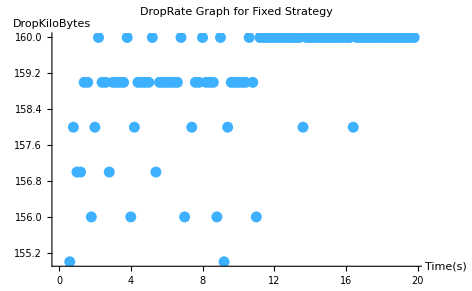

```mathematica
ListPlot[time2Drop,
PlotLabel-> "DropRate Graph for "<>strategyName<>" Strategy" ,
AxesLabel->{"Time(s)","DropKiloBytes"},
PlotStyle->96
]
```

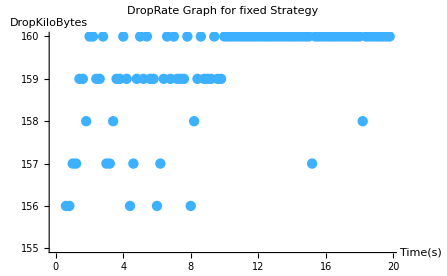
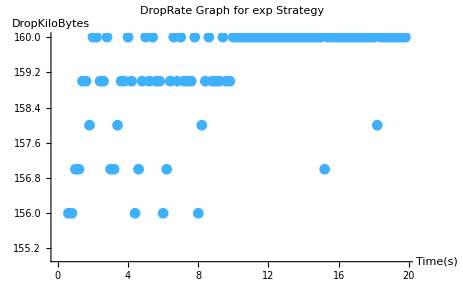

{-Graphics-,-Graphics-}

```mathematica
allNodeDrop = Table[
ListPlot[
time2DropAll⟦i+1⟧,
PlotLabel-> strategyName<>" Strategy: " <>"Node-"<>ToString[i],
AxesLabel->{"Time(s)","DropKiloBytes"},
PlotStyle->96
]
,{i,0,8}
]
```